I need a way to normalize polygons to a list of percentages to apply as a clip path to elements, I’ll try hexagons first.
Take the points, find the bounding box, recalculate each point as a ratio of the bounding box. The bounding box of a circle with radius 1 is a square with side length 2 -- relative to what? Coordinate system is bottom left of bounding box, 0 0 is bottom left, 100 100 is top right. So basically we just need to translate the center of the circle into the center of our positive quadrant

```mathematica
1-(√3)/2 // N
```

0.133975

```mathematica
CirclePoints[{1,1},{1,0},6]
```

{{2,1},{3/2,1+(√3)/2},{1/2,1+(√3)/2},{0,1},{1/2,1-(√3)/2},{3/2,1-(√3)/2}}

```mathematica
Map[ScalingTransform[{0.5,0.5},{1,1}],CirclePoints[{1,1},{1,0},6]]
```

{{1.5,1.},{1.25,1.43301},{0.75,1.43301},{0.5,1.},{0.75,0.566987},{1.25,0.566987}}

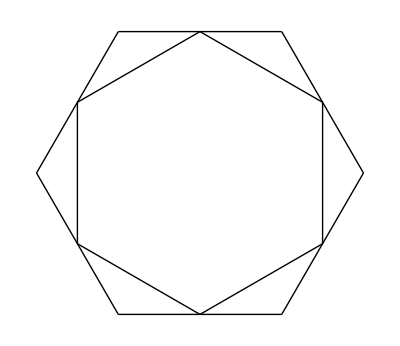

```mathematica
Graphics[{
Line /@ Partition[CirclePoints[{1,1},{1, 0},6], 2, 1, {1}] ,
Line /@ Partition[Map[ScalingTransform[{Sqrt[3]/2,Sqrt[3]/2},{1,1}],CirclePoints[{1,1},{1, Pi/2},6]], 2, 1, {1}] 
}]
```

```mathematica
CirclePoints[{1,1},{1,0},6]
```

{{2,1},{3/2,1+(√3)/2},{1/2,1+(√3)/2},{0,1},{1/2,1-(√3)/2},{3/2,1-(√3)/2}}

```mathematica
Export["circles.json",Map[N, CirclePoints[{1,1},{1,0},6], {2}]]
```

circles.json

```mathematica
Export["circles.json",StringJoin[#1, " ", #2] & @@@ Map[StringJoin[ToString[N[#*50]],"0%"] &,CirclePoints[{1,1},{1,0},6],{2}]]
```

circles.json

```mathematica
Graphics[{
Point /@ {{0,0},{0,1},{1,1},{1,0}},
Point /@ Map[N[#/2] &,CirclePoints[{1,1},{1,0},6],{2}]
}]
```

-Graphics-

```mathematica
|
```

```mathematica
100.% 50.%,75.% 93.3013%,25.% 93.3013%,0.% 50.%,25.% 6.69873%,75.% 6.69873%
```

```mathematica
triangles[3]
```

{{-9/2,-(3 √3)/2},{-4,-√3},{-7/2,-(√3)/2},{-3,0},{-5/2,(√3)/2},{-2,√3},{-3/2,(3 √3)/2},{-7/2,-(3 √3)/2},{-3,-√3},{-5/2,-(√3)/2},{-2,0},{-3/2,(√3)/2},{-1,√3},{-1/2,(3 √3)/2},{-5/2,-(3 √3)/2},{-2,-√3},{-3/2,-(√3)/2},{-1,0},{-1/2,(√3)/2},{0,√3},{1/2,(3 √3)/2},{-3/2,-(3 √3)/2},{-1,-√3},{-1/2,-(√3)/2},{0,0},{1/2,(√3)/2},{1,√3},{3/2,(3 √3)/2},{-1/2,-(3 √3)/2},{0,-√3},{1/2,-(√3)/2},{1,0},{3/2,(√3)/2},{2,√3},{5/2,(3 √3)/2},{1/2,-(3 √3)/2},{1,-√3},{3/2,-(√3)/2},{2,0},{5/2,(√3)/2},{3,√3},{7/2,(3 √3)/2},{3/2,-(3 √3)/2},{2,-√3},{5/2,-(√3)/2},{3,0},{7/2,(√3)/2},{4,√3},{9/2,(3 √3)/2}}

To draw polygons over a lattice I’m taking the tuples returned by trianlges[] and using them as the center of a circle, supplying radius and spin of the circle, and then grabbing all consecutive (+ wraparound) points to get 2-tuples of points to draw their lines into graphics.

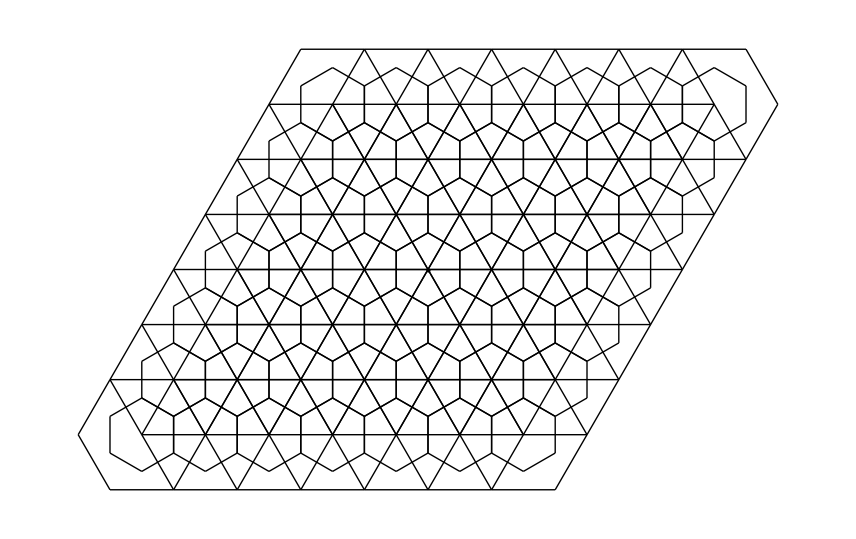

```mathematica
Graphics[{
Point[{0,0}],
Line/@ Partition[CirclePoints[#,{Sqrt[3]/3, Pi/6},6], 2, 1, {1}] & /@ triangles[3],
Line/@ Partition[CirclePoints[#,{1, 0},6], 2, 1, {1}] & /@ triangles[3]
}]
```

```mathematica
Sqrt[3]/3 // N
```

0.57735

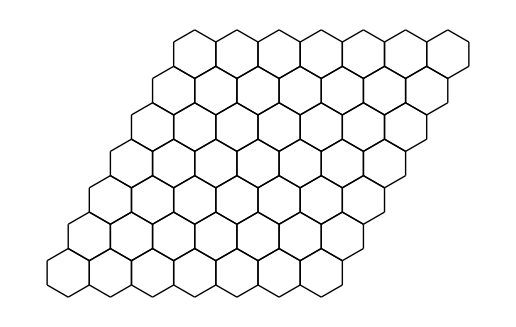

```mathematica
Graphics[{
Line/@ Partition[CirclePoints[#,{Sqrt[3]/3, Pi/6},6], 2, 1, {1}] & /@ triangles[3]
}]
```